```mathematica
Eqn = y'''[x]+3y''[x]+4y'[x]+12y[x]
```

12 y[x]+4 y'[x]+3 y''[x]+y^(3)[x]

```mathematica
Sol = DSolve[{Eqn ==0, y''[0]==0,y'[0]==a,y[0]==0},y[x],x]
```

{{y[x]→1/2 a Sin[2 x]}}

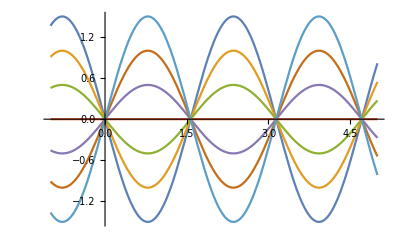

```mathematica
Plot[Evaluate[y[x]/.Sol/.a->{-3,-2,-1,0,1,2,3}],{x,-1,5}]
```

```mathematica
Solution = DSolve[{Eqn ==0, y''[0]==0,y'[0]==0,y[0]==b},y[x],x]
```

{{y[x]→1/13 b ⅇ^(-3 x) (4+9 ⅇ^(3 x) Cos[2 x]+6 ⅇ^(3 x) Sin[2 x])}}

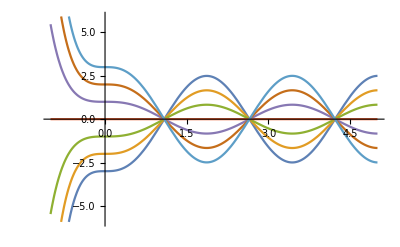

```mathematica
Plot[Evaluate[y[x]/.Solution/.b->{-3,-2,-1,0,1,2,3}],{x,-1,5}]
```

```mathematica
value = DSolve[{Eqn ==0, y''[0]==a,y'[0]==0,y[0]==0},y[x],x]
```

{{y[x]→-1/26 a ⅇ^(-3 x) (-2+2 ⅇ^(3 x) Cos[2 x]-3 ⅇ^(3 x) Sin[2 x])}}

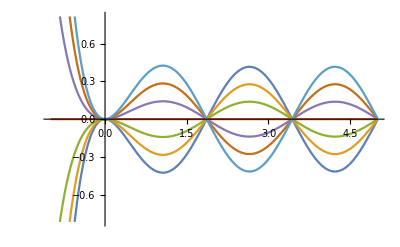

```mathematica
Plot[Evaluate[y[x]/.value/.a->{-3,-2,-1,0,1,2,3}],{x,-1,5}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
first = x'[t]-n*x[t]
```

-n x[t]+x'[t]

```mathematica
Ans = DSolve[{first ==0,x[0]==C},x[t],t]
```

{{x[t]→C ⅇ^(n t)}}

```mathematica
Plot[Evaluate[x[t]/.Ans/.{n->2,C->6}],{t,1,40}]
```

-Graphics-

```mathematica
Evaluate[x[t]/.Ans/.{n->2,C->6,t->51}]
```

{6 ⅇ^102}

```mathematica
first = P'[t]-n*P[t]
```

-n P[t]+P'[t]

```mathematica
Ans = DSolve[{first ==0,P[0]==C},P[t],t]
```

{{P[t]→C ⅇ^(n t)}}

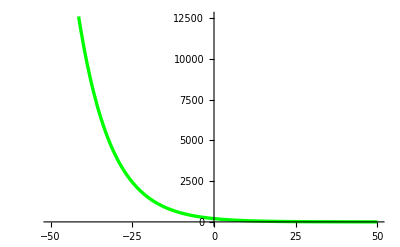

```mathematica
Plot[Evaluate[P[t]/.Ans/.{C->200,n->-0.1}],{t,-50,50},PlotStyle->{Green,Thickness[0.006]}]
```

```mathematica
Evaluate[P[t]/.Ans/.{C->200,n->-0.1,t->1.5}]
```

{172.142}

#### Lake pollution model with constant flow and pollution concentration

C'[t]==25/14 (3-C[t])

{{C[t]→ⅇ^(-25 t/14) (-3+c0+3 ⅇ^(25 t/14))}}

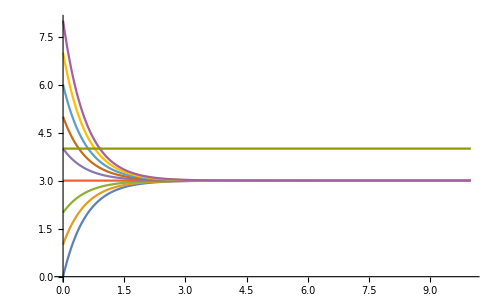

```mathematica
cin = 3;
V = 28;
F=50;
threshold = 4;
de1 = D[C[t],t]==(F/V)*(cin-C[t])
soln = DSolve[{de1,C[0]==c0},C[t],t]
plot1 = Plot[{Evaluate[C[t]/.soln/.c0->Range[0,8]],threshold},{t,0,10},PlotRange->{0,8}]
```

#### Example of lake Erie in America:

```mathematica
cin = 0;
V = 458*10^9;
F=480*10^6;
de1 = D[C[t],t]==(F/V)*(cin-C[t])
soln = DSolve[{de1,C[0]==c0},C[t],t]
C[t]/.First[soln]
sol = Solve[%==0.05*c0,t]
Print["Years = ", N[{t/.sol[[1]]}/365]]
```

C'[t]==-(6 C[t])/5725

{{C[t]→c0 ⅇ^(-6 t/5725)}}

c0 ⅇ^(-6 t/5725)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→2858.43}}

Years = {7.83131}

### Example of lake Ontario in America

```mathematica
cin = 0;
V = 1636*10^9;
F=572*10^6;
de1 = D[C[t],t]==(F/V)*(cin-C[t])
soln = DSolve[{de1,C[0]==c0},C[t],t]
C[t]/.First[soln]
sol = Solve[%==0.05*c0,t]
Print["Years = ", N[{t/.sol[[1]]}/365]]
```

C'[t]==-(143 C[t])/409000

{{C[t]→c0 ⅇ^(-143 t/409000)}}

c0 ⅇ^(-143 t/409000)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→8568.21}}

Years = {23.4746}